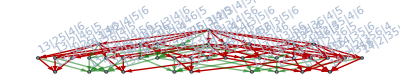

```mathematica
Graph[FormulaGraph[allGraphs6[5039100,"colofour"]],ImageSize->{Automatic,220},EdgeStyle->Directive[Opacity[0.5],Darker[Darker[Green]]],
GraphHighlight->EdgeList[FormulaGraph[allGraphs6[5039829,"colofour"]]]]
```

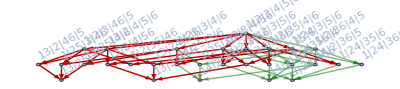

```mathematica
Graph[FormulaGraph[allGraphs6[5039829,"colofour"]],ImageSize->{Automatic,220},EdgeStyle->Directive[Opacity[0.5],Darker[Darker[Green]]],
GraphHighlight->EdgeList[FormulaGraph[allGraphs6[5039856,"colofour"]]]]
```

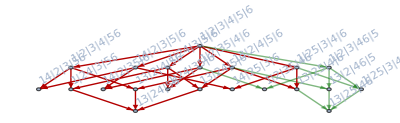

```mathematica
Graph[FormulaGraph[allGraphs6[5039856,"colofour"]],ImageSize->{Automatic,220},EdgeStyle->Directive[Opacity[0.5],Darker[Darker[Green]]],
GraphHighlight->EdgeList[FormulaGraph[allGraphs6[5039859,"colofour"]]]]
```

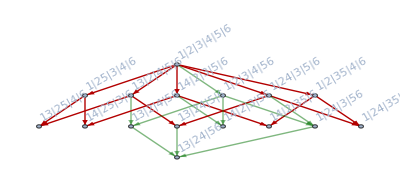

```mathematica
Graph[FormulaGraph[allGraphs6[5039859,"colofour"]],ImageSize->{Automatic,220},EdgeStyle->Directive[Opacity[0.5],Darker[Darker[Green]]],
GraphHighlight->EdgeList[FormulaGraph[allGraphs6[5039860,"colofour"]]]]
```

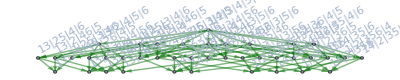
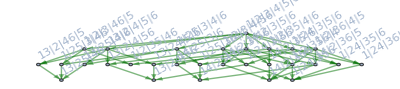
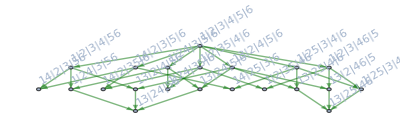
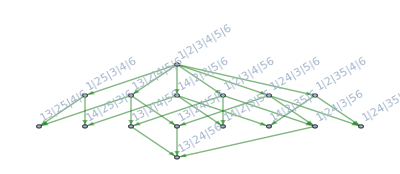
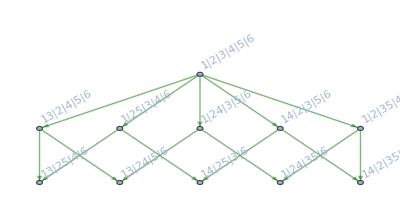
-Graphics-5039100→-Graphics-
-Graphics-5039829→-Graphics-
-Graphics-5039856→-Graphics-
-Graphics-5039859→-Graphics-
-Graphics-5039860→-Graphics-

```mathematica
Table[
Table[Labeled[allGraphs6[k,"graph"],Style[k,Red,Underlined]]-> Graph[FormulaGraph[allGraphs6[k,"colofour"]],ImageSize->{Automatic,180},EdgeStyle->Directive[Opacity[0.5],Darker[Darker[Green]]]],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexDegree[g,6]==m&&Fold[And,Table[EdgeQ[g,w<->6],{w,m}]]
&& EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,1<->5]&&EdgeCount[g]==5+m]&]}]
,{m,1,5}]//TableForm
```